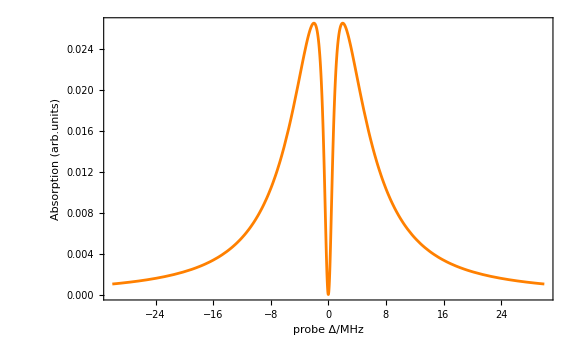

```mathematica
Γ13=2*π*(6-I*Δ13);
Γ12=2*π*(0-I*(Δ13-Δ23));
χ[Δ13_,Δ23_,Ω23_]=I/Γ13*Γ12/(Γ12+Ω23^2/Γ13);
Plot[Im[χ[Δ13,0,2*π*2]],{Δ13,-30,30},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{{Style["Absorption (arb.units)",20,Black],None},{Style["probe Δ/MHz",20,Black],None}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->20,ImageSize->Large]
```

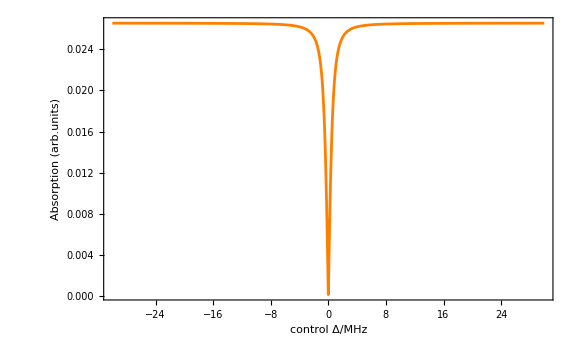

```mathematica
Plot[Abs[χ[2 π*0,Δ12,2*π*2]],{Δ12,-30,30},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{{Style["Absorption (arb.units)",20,Black],None},{Style["control Δ/MHz",20,Black],None}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->20,ImageSize->Large,PlotRange->All]
```

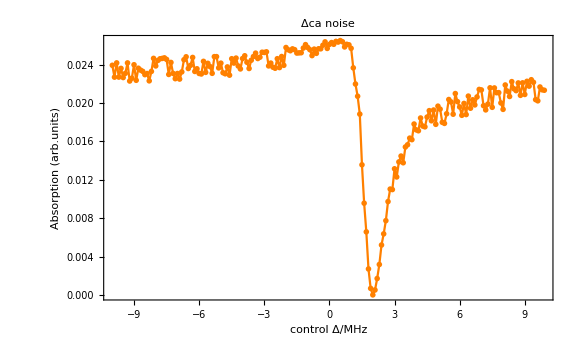

0.496975

```mathematica
list1={};
For[Δ12=-10,Δ12<10,Δ12=Δ12+0.1,
noise=RandomReal[];
AppendTo[list1,{Δ12,Im[χ[2+noise,Δ12+noise,2*π*2]]}]
];

ListPlot[list1,PlotRange->All,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{{Style["Absorption (arb.units)",20,Black],None},{Style["control Δ/MHz",20,Black],None}},PlotLabel->"Δca noise",FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->20,ImageSize->Large]
```